# Billiards Dynamics

### Functions

```mathematica
ClearAll[bounce];
Options[bounce]={"PhaseSpace"->False};
bounce[point_?VectorQ,direction_?VectorQ,δ_?NumericQ,OptionsPattern[]]:=Module[
{sol,normalized,nextpoint,nextdirection,ϕ},
	sol=NSolve[{{𝓍[θ,δ],𝓎[θ,δ]}==point+t*direction ,Abs[t]>10^-10,0≤θ<2 π},{t,θ},Reals]//Quiet;
	sol=If[Length@sol>0,First@sol,Return[$Failed,Module]];
	nextpoint={𝓍[θ,δ],𝓎[θ,δ]}/.sol;
	ϕ=ArcTan[D[𝓎[θ,δ],θ]/D[𝓍[θ,δ],θ]/. sol];
	nextdirection=RotationTransform[ϕ][ReflectionTransform[{0,1}][RotationTransform[-ϕ][Normalize[N@direction]]]];
	If[OptionValue["PhaseSpace"],
		{nextpoint,nextdirection,ArcLength[{𝓍[φ,δ],𝓎[φ,δ]},{φ,0,#}],Sin@VectorAngle[nextdirection,tangentvector[#,δ]]}&@(θ/.sol),
		{nextpoint,nextdirection}
	]
]
```

```mathematica
ClearAll[bounceEvolution];
Options[bounceEvolution]={"PhaseSpace"->False,"Bounces"->100};
bounceEvolution[point_?VectorQ,direction_?VectorQ,δ_?NumericQ,OptionsPattern[]]:=Module[{result},
	result=NestList[
		bounce[#[[1]],#[[2]],δ,"PhaseSpace"->OptionValue["PhaseSpace"]]&,
		{point,direction},
		OptionValue["Bounces"]
		];
	
	If[OptionValue["PhaseSpace"],
	<|"Result"->result[[All,;;2]],"PhaseSpace"->Drop[result,1][[All,3;;]]|>,
	result
	]
	
]
```

```mathematica
ClearAll[tangentvector];
tangentvector[θ_,δ_]:=Simplify[(D[r[Θ,δ],Θ]/Norm[D[r[Θ,δ],Θ]])/.Θ->θ,θ∈Reals]
```

```mathematica
ClearAll[r];
r[θ_,δ_]:={𝓍[θ,δ],𝓎[θ,δ]}
```

## Circle

Parametrization

```mathematica
ClearAll[𝓍,𝓎]
𝓍[θ_,δ_]:=Cos[θ];
𝓎[θ_,δ_]:=Sin[θ];
```

### Closed paths

```mathematica
regcircle1=ParametricRegion[{𝓍[θ,0],𝓎[θ,0]},{{θ,0,2π}}];
```

```mathematica
{point1,direction1}={{1,0},{1,0}};
horizontalcircle=bounceEvolution[point1,direction1,0,"Bounces"->5,"PhaseSpace"->True];//AbsoluteTiming
```

{3.17286,Null}

```mathematica
{point2,direction2}={{-1,0},AngleVector[π/3]};
closedcircle=bounceEvolution[point2,direction2,0,"Bounces"->20,"PhaseSpace"->True];//AbsoluteTiming
```

{19.3309,Null}

Evolution graphics:

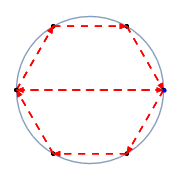

```mathematica
img1=Graphics[{Point/@(#),{Red,Dashed,Arrow[Partition[#,2,1]]},{Blue,Point@point1}}]&@horizontalcircle["Result"][[All,1]];
img2=Graphics[{Point/@(#),{Red,Dashed,Arrow[Partition[#,2,1]]},{Blue,Point@point1}}]&@closedcircle["Result"][[All,1]];Show[{Region@regcircle1,img2,img1},ImageSize->Small]
```

Birkhoff phase-space

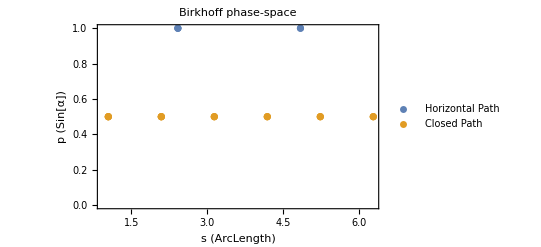

```mathematica
ListPlot[{horizontalcircle["PhaseSpace"],closedcircle["PhaseSpace"]},PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space",PlotLegends->{"Horizontal Path","Closed Path"}]
```

### Star path

```mathematica
regcircle1=ParametricRegion[{𝓍[θ,0],𝓎[θ,0]},{{θ,0,2π}}];
```

```mathematica
{point3,direction3}={{1,0},AngleVector[π/8]};
starcircle=bounceEvolution[point3,direction3,0,"Bounces"->60,"PhaseSpace"->True];//AbsoluteTiming
```

{49.7538,Null}

Evolution graphics:

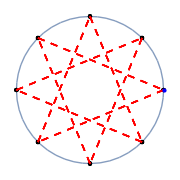

```mathematica
img3=Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@point3}}]&@starcircle["Result"][[All,1]];Show[{Region@regcircle1,img3},ImageSize->Small]
```

Birkhoff phase-space

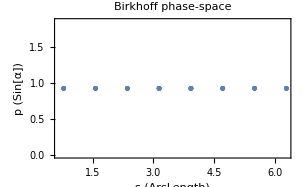

```mathematica
ListPlot[starcircle["PhaseSpace"],PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space"]
```

### Circulating path

```mathematica
regcircle1=ParametricRegion[{𝓍[θ,0],𝓎[θ,0]},{{θ,0,2π}}];
```

```mathematica
{point3,direction3}={{1+0.1,0},AngleVector[π/7]};
allcircle=bounceEvolution[point3,direction3,0,"Bounces"->60,"PhaseSpace"->True];//AbsoluteTiming
```

{51.5082,Null}

Evolution graphics:

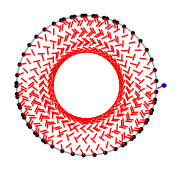

```mathematica
img3=Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@point3}}]&@allcircle["Result"][[All,1]];Show[{Region@regcircle1,img3},ImageSize->Small]
```

Birkhoff phase-space

```mathematica
ListPlot[allcircle["PhaseSpace"],PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space"]
```

-Graphics-

### Magnification

General - Phase Space

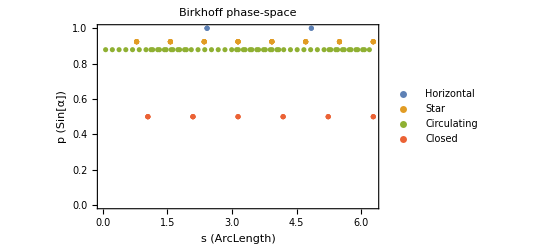

```mathematica
ListPlot[{horizontalcircle["PhaseSpace"],starcircle["PhaseSpace"],allcircle["PhaseSpace"],closedcircle["PhaseSpace"]},]
```

Fig 12.2: Introduction to Billiard Dynamics (pp 171–180) https://link.springer.com/chapter/10.1007/978-981-16-3544-1_12

## Ellipse

Parametrization

```mathematica
ClearAll[a,b,𝓍,𝓎]
a=1;b=.5;
𝓍[θ_,δ_]:=a*Cos[θ];
𝓎[θ_,δ_]:=b*Sin[θ];
```

### Closed paths

```mathematica
ellipse1=ParametricRegion[{𝓍[θ,0],𝓎[θ,0]},{{θ,0,2π}}];
```

```mathematica
{point4,direction4}={{1,0},AngleVector[0]};
ellipseresult1=bounceEvolution[point4,direction4,0,"Bounces"->5,"PhaseSpace"->True];//AbsoluteTiming
```

{3.08239,Null}

Evolution graphics:

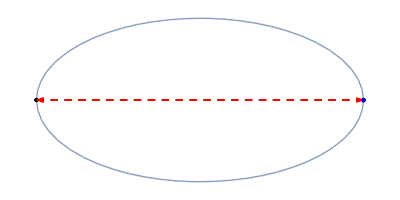

```mathematica
imgellipse=Graphics[{Point/@(#),{Red,Dashed,Arrow[Partition[#,2,1]]},{Blue,Point@point4}}]&@ellipseresult1["Result"][[All,1]];
Show[{Region@ellipse1,imgellipse}]
```

Birkhoff phase-space

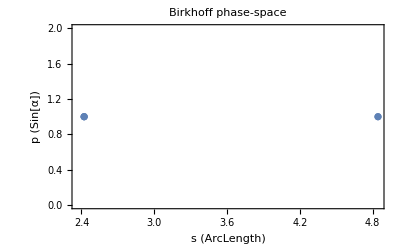

```mathematica
ListPlot[ellipseresult1["PhaseSpace"],PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space"]
```

### Rotation paths

```mathematica
ellipse1=ParametricRegion[{𝓍[θ,0],𝓎[θ,0]},{{θ,0,2π}}];
```

```mathematica
{point5,direction5}={{1,0},AngleVector[π/4]};
ellipseresult2=bounceEvolution[point5,direction5,0,"Bounces"->60,"PhaseSpace"->True];//AbsoluteTiming
```

{52.4414,Null}

Evolution graphics:

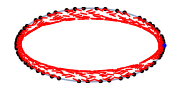

```mathematica
img5=Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@point5}}]&@ellipseresult2["Result"][[All,1]];Show[{Region@ellipse1,img5},ImageSize->Small]
```

Birkhoff phase-space

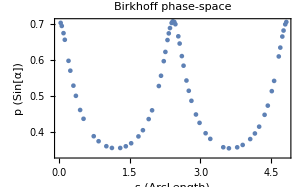

```mathematica
ListPlot[ellipseresult2["PhaseSpace"],PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space"]
```

#### Extra orbits

```mathematica
{point51,direction51}={{0,0.5},AngleVector[-π/8]};
ellipseresult21=bounceEvolution[point51,direction51,0,"Bounces"->60,"PhaseSpace"->True];//AbsoluteTiming
```

{53.6204,Null}

Evolution graphics:

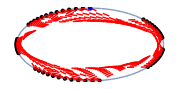

```mathematica
img51=Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@point51}}]&@ellipseresult21["Result"][[All,1]];Show[{Region@ellipse1,img51},ImageSize->Small]
```

Birkhoff phase-space

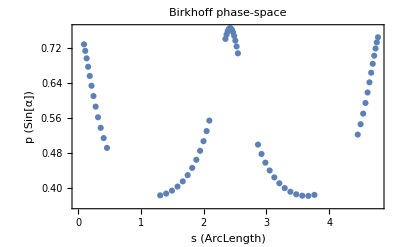

```mathematica
ListPlot[ellipseresult21["PhaseSpace"],PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space"]
```

### Libration paths

```mathematica
ellipse1=ParametricRegion[{𝓍[θ,0],𝓎[θ,0]},{{θ,0,2π}}];
```

```mathematica
{point6,direction6}={{0,0.5},AngleVector[π/4]};
ellipseresult3=bounceEvolution[point6,direction6,0,"Bounces"->60,"PhaseSpace"->True];//AbsoluteTiming
```

{50.0065,Null}

Evolution graphics:

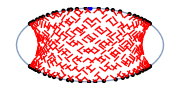

```mathematica
img6=Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@point6}}]&@ellipseresult3["Result"][[All,1]];Show[{Region@ellipse1,img6},ImageSize->Small]
```

Birkhoff phase-space

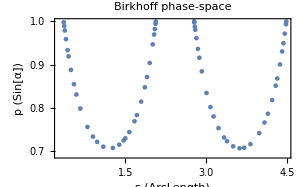

```mathematica
ListPlot[ellipseresult3["PhaseSpace"],PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space"]
```

### Magnification

Constant of motion:

```mathematica
ϵ=√(1-b^2/a^2);
F[θ_,p_]:=(p^2-ϵ^2 Cos[θ]^2)/(1-ϵ^2 Cos[θ]^2)
```

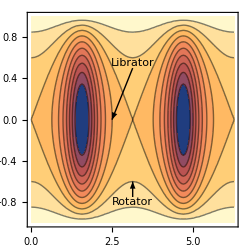

```mathematica
ContourPlot[F[θ,p],{θ,0,2π},{p,-1,1},]
```

Fig.1: Scattering Dynamics of Driven Closed Billiards (https://arxiv.org/pdf/0705.1126 )

Fig 7: Three deformations of a circular ‘billiard’ - M. Berry (https://iopscience.iop.org/article/10.1088/0143-0807/2/2/006 )

General - Phase Space:

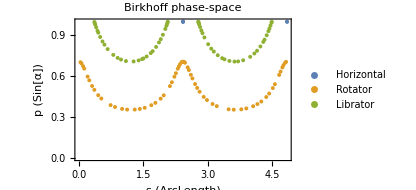

```mathematica
ListPlot[{ellipseresult1["PhaseSpace"],ellipseresult2["PhaseSpace"],ellipseresult3["PhaseSpace"]},]
```

#### Cos[α]

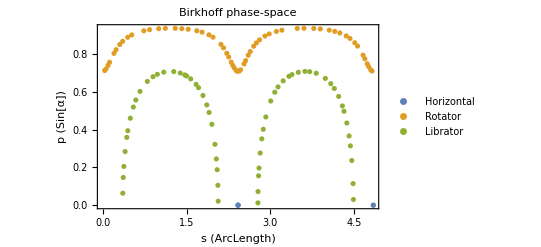

```mathematica
newpointsellipse=MapAt[√(1-#^2)&,#,{All,2}]&/@{ellipseresult1["PhaseSpace"],ellipseresult2["PhaseSpace"],ellipseresult3["PhaseSpace"]};
ListPlot[newpointsellipse,]
```

## Oval

Parametrization

```mathematica
ClearAll[𝓍,𝓎]
𝓍[θ_,δ_]:=Sin[θ]+δ/2 Sin[θ]+δ/6 Sin[3θ];
𝓎[θ_,δ_]:=-Cos[θ]+δ/2 Cos[θ]-δ/6 Cos[3θ];
```

### Unstable circulating 4-bounce orbit

```mathematica
δ1=0.3;
reg1=ParametricRegion[{𝓍[θ,δ1],𝓎[θ,δ1]},{{θ,0,2π}}];
{initPosition1,initDirection1}={{𝓍[π/2,δ1],𝓎[π/2,δ1]},{-𝓍[π/2,δ1],𝓎[π,δ1]}};
```

```mathematica
result1=bounceEvolution[initPosition1,initDirection1,δ1,"Bounces"->600,"PhaseSpace"->True];//AbsoluteTiming
```

{29.6903,Null}

Evolution graphics: 10 steps and 600 steps

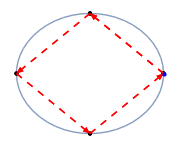

```mathematica
img1={Region@reg1,Graphics[{Point/@(#),{Red,Dashed,Arrow[Partition[#,2,1]]},{Blue,Point@initPosition1}}]}&@result1["Result"][[;;10,1]];Show[img1,ImageSize->Small]
```

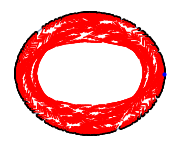

```mathematica
Show[{Region@reg1,Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@initPosition1}}]},ImageSize->Small]&@result1["Result"][[All,1]]
```

Birkhoff phase-space

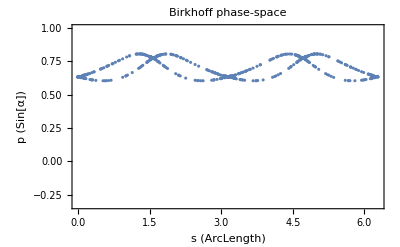

```mathematica
ListPlot[result1["PhaseSpace"],PlotRange->{{0,2π},{-0.33,1}},Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space",Epilog->{Inset[Show[img1,ImageSize->Tiny],{3.2,0.1}]}]
```

### Stable circulating 4-bounce orbit

```mathematica
δ1=0.3;
reg1=ParametricRegion[{𝓍[φ,δ1],𝓎[φ,δ1]},{{φ,0,2π}}];
{initPosition2,initDirection2}={{𝓍[π/4,δ1],𝓎[π/4,δ1]},{0.01,𝓎[π/4,δ1]}};
```

```mathematica
result2=bounceEvolution[initPosition2,initDirection2,δ1,"Bounces"->600,"PhaseSpace"->True];//AbsoluteTiming
```

{28.3742,Null}

Evolution graphics: 10 steps and 600 steps

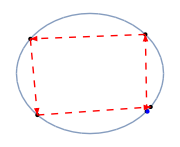

```mathematica
img2={Region@reg1,Graphics[{Point/@(#),{Red,Dashed,Arrow[Partition[#,2,1]]},{Blue,Point@initPosition2}}]}&@result2["Result"][[;;5,1]];Show[img2,ImageSize->Small]
```

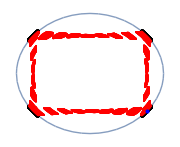

```mathematica
Show[{Region@reg1,Graphics[{Point/@(#),{Red,Dashed,Line[Partition[#,2,1]]},{Blue,Point@initPosition2}}]},ImageSize->Small]&@result2["Result"][[All,1]]
```

Birkhoff phase-space

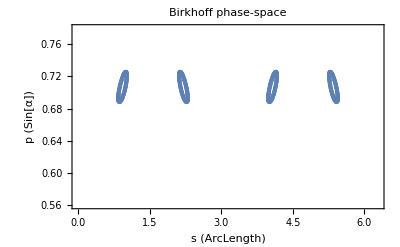

```mathematica
ListPlot[result2["PhaseSpace"],PlotRange->{{0,2π},{0.56,0.78}},Axes->False,Frame->True,FrameLabel->{"s (ArcLength)","p (Sin[α])"},PlotLabel->"Birkhoff phase-space",Epilog->{Inset[Show[img2,ImageSize->Tiny],{3.2,0.62}]}]
```

### Complementary orbits

```mathematica
δ1=0.3;
reg1=ParametricRegion[{𝓍[φ,δ1],𝓎[φ,δ1]},{{φ,0,2π}}];
```

“Outer” orbit

```mathematica
{initPosition3,initDirection3}={{𝓍[π/4,δ1],𝓎[π/4,δ1]},{0.01,𝓎[π/4,δ1]+0.1}};
result3=bounceEvolution[initPosition3,initDirection3,δ1,"Bounces"->600,"PhaseSpace"->True];//AbsoluteTiming
```

{29.7024,Null}

“Inner” orbit

```mathematica
{initPosition4,initDirection4}={{𝓍[π/4,δ1],𝓎[π/4,δ1]},{0.001,𝓎[π/4,δ1]}};
result4=bounceEvolution[initPosition4,initDirection4,δ1,"Bounces"->600,"PhaseSpace"->True];//AbsoluteTiming
```

{29.4854,Null}

“Dashed” orbit (should be an island chain)

```mathematica
{initPosition5,initDirection5}={{𝓍[π/4,δ1],𝓎[π/4,δ1]},{0.03,𝓎[π/4,δ1]}};
result5=bounceEvolution[initPosition5,initDirection5,δ1,"Bounces"->600,"PhaseSpace"->True];//AbsoluteTiming
```

{30.0393,Null}

“Transition” orbit

```mathematica
{initPosition6,initDirection6}={{𝓍[π/4,δ1],𝓎[π/4,δ1]},{-0.056,𝓎[π/4,δ1]}};
result6=bounceEvolution[initPosition6,initDirection6,δ1,"Bounces"->600,"PhaseSpace"->True];//AbsoluteTiming
```

{30.0747,Null}

### Magnification

```mathematica
results={result1,result2,result3,result4,result5,result6};
```

General Birkhoff phase-space

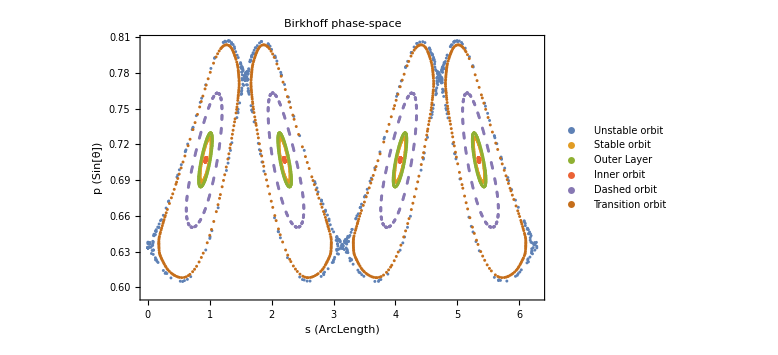

```mathematica
ListPlot["PhaseSpace"/.results,]
```

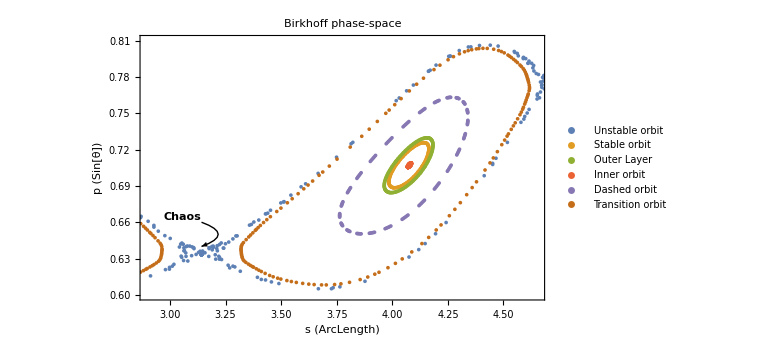

```mathematica
ListPlot["PhaseSpace"/.results,PlotRange->{{2.9,4.65},{0.6,0.81}},]
```